```mathematica
Directory[]
```

C:\Users\A_suozhang\Documents

```mathematica
file = Import["C:\\Users\\A_suozhang\\Code\\EE\\Verilog\\Read_Text\\test_re.txt","Data"];
```

```mathematica
file[[All, 1]];
Part[file,2,1];
file[[1;;3]];
dats = Interpreter["Binary"][file[[All,1]]]
```

{664,{48,48,48,54,102,57},956,1158,{48,48,99,57,98,57},{102,102,101,57,56,52},{102,102,102,52,57,57},{102,102,102,55,102,50},{102,102,102,57,56,55},{102,102,102,97,54,57},{102,102,102,97,102,56},{102,102,102,98,53,99},{102,102,102,98,97,55},{102,102,102,98,100,56},{102,102,102,99,48,48},{102,102,102,99,50,48},{102,102,102,99,51,98},{102,102,102,99,53,50},{102,102,102,99,54,49},{102,102,102,99,54,100},{102,102,102,99,55,98},{102,102,102,99,56,50},{102,102,102,99,56,99},{102,102,102,99,57,53},{102,102,102,99,57,97},{102,102,102,99,97,49},{102,102,102,99,97,52},{102,102,102,99,97,101},{102,102,102,99,97,100},{102,102,102,99,98,53},{102,102,102,99,98,53},{102,102,102,99,98,98},{102,102,102,99,98,98},{102,102,102,99,98,101},{102,102,102,99,98,102},{102,102,102,99,99,48},{102,102,102,99,99,51},{102,102,102,99,99,55},{102,102,102,99,99,55},{102,102,102,99,99,97},{102,102,102,99,99,100},{102,102,102,99,99,57},{102,102,102,99,99,57},{102,102,102,99,99,100},{102,102,102,99,99,100},{102,102,102,99,99,100},{102,102,102,99,99,101},{102,102,102,99,100,50},{102,102,102,99,100,48},{102,102,102,99,100,48},{102,102,102,99,100,98},{102,102,102,99,100,49},{102,102,102,99,99,101},{102,102,102,99,100,52},{102,102,102,99,100,54},{102,102,102,99,100,53},{102,102,102,99,100,50},{102,102,102,99,100,51},{102,102,102,99,100,55},{102,102,102,99,100,51},{102,102,102,99,100,56},{102,102,102,99,100,50},{102,102,102,99,100,54},{102,102,102,99,100,57},{102,102,102,99,100,54},{102,102,102,99,100,97},{102,102,102,99,100,55},{102,102,102,99,100,51},{102,102,102,99,100,56},{102,102,102,99,100,50},{102,102,102,99,100,56},{102,102,102,99,100,52},{102,102,102,99,100,51},{102,102,102,99,100,53},{102,102,102,99,100,55},{102,102,102,99,100,51},{102,102,102,99,99,102},{102,102,102,99,100,49},{102,102,102,99,100,100},{102,102,102,99,100,49},{102,102,102,99,100,48},{102,102,102,99,100,51},{102,102,102,99,99,102},{102,102,102,99,99,101},{102,102,102,99,99,101},{102,102,102,99,99,102},{102,102,102,99,99,98},{102,102,102,99,99,97},{102,102,102,99,99,101},{102,102,102,99,99,99},{102,102,102,99,99,57},{102,102,102,99,99,55},{102,102,102,99,99,52},{102,102,102,99,99,48},{102,102,102,99,99,48},{102,102,102,99,99,48},{102,102,102,99,98,98},{102,102,102,99,98,100},{102,102,102,99,98,54},{102,102,102,99,98,55},{102,102,102,99,97,101},{102,102,102,99,98,48},{102,102,102,99,97,54},{102,102,102,99,97,51},{102,102,102,99,57,97},{102,102,102,99,57,54},{102,102,102,99,56,102},{102,102,102,99,56,52},{102,102,102,99,55,99},{102,102,102,99,54,101},{102,102,102,99,54,50},{102,102,102,99,53,49},{102,102,102,99,51,98},{102,102,102,99,49,102},{102,102,102,99,48,50},{102,102,102,98,100,97},{102,102,102,98,97,55},{102,102,102,98,53,102},{102,102,102,97,102,100},{102,102,102,97,54,99},{102,102,102,57,56,55},{102,102,102,55,102,53},{102,102,102,52,57,101},{102,102,101,57,56,56},{48,48,99,57,98,57},{48,48,49,49,53,100},959,{48,48,48,54,102,97}}

This is a Comment

```mathematica
dats[[1]]
```

664

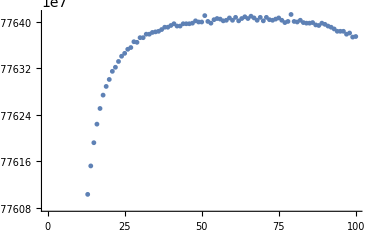

```mathematica
ListPlot[Table[{i, dats[[i]]},{i,0,100}]]
```

```mathematica
Table[{i,i+i},{i,0,4}]
```

{{0,0},{1,2},{2,4},{3,6},{4,8}}

```mathematica
BaseForm[ff,10]
```

ff

```mathematica
IntegerString[-100,16]
```

64